# 1 - D finite Square Potential Well

```mathematica
V[x] = {{{-V,           -a<x<a}, {0, x ∈otherwise}}
```

## Schrödinger approch

```mathematica
(* the Schrödinger equation *)
-ℏ^2/(2m)(Ψ^(2,0))[x,t]+V[x] Ψ[x,t]=ⅈ ℏ (Ψ^(0,1))[x,t]
```

```mathematica
(* Seprattion of varible *)
Ψ[x,t]= ψ[x] T[t]
-ℏ^2/(2m)ψ''[x]/ψ[x]+V[x] =ⅈ ℏ  T'[t]/T[t]
```

```mathematica
(* 2 equations *)
ⅈ ℏ  T'[t] = Ε T[t]
-ℏ^2/(2m)ψ''[x] +V[x] ψ[x]= Ε ψ[x]
```

```mathematica
(* The time component *)
DSolve[{T'[t] == -ⅈ Ε/ℏ T[t],T[0]==1},T[t],t]
```

{{T[t]→ⅇ^(-(ⅈ t Ε)/ℏ)}}

```mathematica
(* The Space component *)
```

```mathematica
-ℏ^2/(2m)ψ''[x] +V[x] ψ[x]= Ε ψ[x]
k0^2=(2m Ε)/ℏ^2 (* For E < 0 , k0 is imaginary *)
k^2=(2 m (Ε+V))/ℏ^2 (* -V < E , k is real *)
```

```mathematica
Collect[DSolve[{ψ1''[x]==- k0^2 ψ1[x],ψ''[x]==- k^2 ψ[x],ψ2''[x]==- k0^2 ψ2[x]},{ψ1[x],ψ[x],ψ2[x]},x]//TrigToExp,{ⅇ^(-ⅈ x ω) ,ⅇ^(ⅈ x ω) ,ⅇ^(ⅈ x ωw) ,ⅇ^(-ⅈ x ωw) }]
```

DSolve::dsfun: ⅇ^ⅈ x ω C[1] cannot be used as a function.

DSolve[{-ⅇ^(ⅈ x ω) ω^2 C[1]==-ⅇ^(ⅈ x ω) k0^2 C[1],-ⅇ^(ⅈ x ωw) ωw^2 C[2]-ⅇ^(-ⅈ x ωw) ωw^2 C[3]==-k^2 (ⅇ^(ⅈ x ωw) C[2]+ⅇ^(-ⅈ x ωw) C[3]),-ⅇ^(-ⅈ x ω) ω^2 C[4]==-ⅇ^(-ⅈ x ω) k0^2 C[4]},{ⅇ^(ⅈ x ω) C[1],ⅇ^(ⅈ x ωw) C[2]+ⅇ^(-ⅈ x ωw) C[3],ⅇ^(-ⅈ x ω) C[4]},x]

```mathematica
(* For -V < E < 0 *)
(* For x< -a *)
ψ1[x_]:=C[1] ⅇ^(x k0) ;
(* -a < x < a *)
ψ[x_]:=C[2] ⅇ^(ⅈ k x)+C[3] ⅇ^(-ⅈ k x);
(* x > a *)
ψ2[x_]:=C[4] ⅇ^(-x k0) ;
```

## -V < E < 0 (Bounded State )

### Odd Solution

```mathematica
(* For Odd Solution *)
Solve[ψ[0]==0,C[3]]
```

{{C[3]→-C[2]}}

```mathematica
(* For x<0 *)
ψ1[x_]:=C[1] ⅇ^(x k0) ;
(* 0 < x < a *)
ψ[x_]:=C[2]Sin[k x];
(* x > a *)
ψ2[x_]:=-C[1] ⅇ^(-x k0) ;
Solve[{ψ2[a]==ψ[a]},C[1]]
```

{{C[1]→-ⅇ^(a k0) C[2] Sin[a k]}}

```mathematica
(* COntinuounity *)
(D[ψ1[x],x]==D[ψ[x],x])/.x->0
(D[ψ2[x],x]==D[ψ[x],x])/.x->a
```

k0 C[1]==k C[2]

ⅇ^(-a k0) k0 C[1]==k C[2] Cos[a k]

#### Energy Level

```mathematica
(* From *)
(ⅇ^(-a k0) k0 C[1]==k C[2] Cos[a k])/.{C[1]->-ⅇ^(a k0) C[2] Sin[a k]}
```

-k0 C[2] Sin[a k]==k C[2] Cos[a k]

```mathematica
(* Recall *)
k0^2=(2m Abs[Ε])/ℏ^2
k^2=(2 m (V-Abs[Ε]))/ℏ^2 
-Tan[a k]==k/k0
√Abs[Ε] Tan[a/ℏ √(2 m (V-Abs[Ε]))]==- √(V-Abs[Ε])
(* set z = a k *)
z^2+ a^2 k0^2= (2 m a^2)/ℏ^2 V = z0^2
⇒ Tan[z]==-1/(√((z0/z)^2-1))
```

```mathematica
Manipulate[Plot[{Tan[ z],-1/(√((z0/z)^2-1))},{z,0,10}],{z0,1,10}]
```

#### Coeffecient

```mathematica
(* Unility *)
∫_-s^-a (C[2] k/k0 ⅇ^(x k0))^2 ⅆx
∫_-a^a (C[2]Sin[k x])^2 ⅆx
```

((ⅇ^(-2 a k0)-ⅇ^(-2 k0 s)) k^2 C[2]^2)/(2 k0^3)

C[2]^2 (a-Sin[2 a k]/(2 k))

```mathematica
Solve[((ⅇ^(-2 a k0)) k^2 C[2]^2)/(2 k0^3)+C[2]^2 (a-Sin[2 a k]/(2 k))==1,C[2]]//Simplify
```

{{C[2]→-1/(√(a+(ⅇ^(-2 a k0) k^2)/(2 k0^3)-Sin[2 a k]/(2 k)))},{C[2]→1/(√(a+(ⅇ^(-2 a k0) k^2)/(2 k0^3)-Sin[2 a k]/(2 k)))}}

### Even Solution

```mathematica
(* For x<0 *)
ψ1[x_]:=C[1] ⅇ^(x k0) ;
(* 0 < x < a *)
ψ[x_]:=C[2]Cos[k x];
ψ2[x_]:=-C[1] ⅇ^(-x k0) ;
Solve[{ψ2[a]==ψ[a]},C[1]]
(* COntinuounity *)
(D[ψ1[x],x]==D[ψ[x],x])/.x->0
(D[ψ2[x],x]==D[ψ[x],x])/.x->a
```

{{C[1]→-ⅇ^(a k0) C[2] Cos[a k]}}

k0 C[1]==0

ⅇ^(-a k0) k0 C[1]==-k C[2] Sin[a k]

#### Energy Level

```mathematica
(ⅇ^(-a k0) k0 C[1]==-k C[2] Sin[a k])/.{C[1]->-ⅇ^(a k0) C[2] Cos[a k]}
```

-k0 C[2] Cos[a k]==-k C[2] Sin[a k]

```mathematica
Tan[ a k ] == k0/k
⇒ Tan[z] = √(z0^2/z^2-1)
```

```mathematica
Manipulate[Plot[{Tan[ z],√((z0/z)^2-1)},{z,0,10}],{z0,0,10}]
```

## E > 0 ( Scattary State )

## Realistic Solution

```mathematica
ℏ=6.626068×10^-34(* m^2 kg/s *);
Subscript[m, e]=9.10938188×10^-31 (* kg *);
Subscript[m, e]/ℏ
```

1374.78

```mathematica
ℏ=1;
m=1374.78;
a=1;
```

```mathematica
Ψ[x,t,1]
```

√2 Cos[0.00358952 t] Sin[π x]

```mathematica
Manipulate[
Plot[Re[Ψ[x,t,n]],{x,0,1},PlotRange->{-√2,√2}],{t,0,200},{n,1,10,1}]
```

## Properties

```mathematica
<Q> = ∫_0^a Conjugate[Ψ] Q[x] Ψ ⅆx
```

```mathematica
X = x
P  = ⅈ ℏ ∂/(∂x)
H = -ⅈ ℏ ∂/(∂t)
```

```mathematica
(* the mean of position *)
∫_0^a ψ[x,1,n] x ψ[x,1,n] ⅆx
```

-(-1-2 n^2 π^2+Cos[2 n π]+2 n π Sin[2 n π])/(4 n^2 π^2)

```mathematica
D[ψ[x,1,n],x]
```

√2 n π Cos[n π x]

```mathematica
(* the mean of momemtum *)
∫_0^a ψ[x,1,n] ⅈ ℏ  ψ'[x,1,n] ⅆx
```

```mathematica
∫_0^1 ⅈ √2 Sin[n π x] √2 n π Cos[n π x]ⅆx
```

ⅈ Sin[n π]^2

## Solution for proton

```mathematica
(*in the well, Sin[k x] or Cos[k x], k^2= 2 m/ℏ^2(E-V)*)
(*outside the well, Exp[-k0 x] , k0^2=(2m)/ℏ^2 E*)
(* k^2=k0^2-U, U = (2m)/ℏ^2 V *)
```

```mathematica
mp=938.272; (* MeV/c^2*)
ℏ=197.3269788; (* MeV fm*)
a=10 ;(* fm*)
V=55; (* MeV*)
U = (2 mp)/ℏ^2 V
```

2.65063

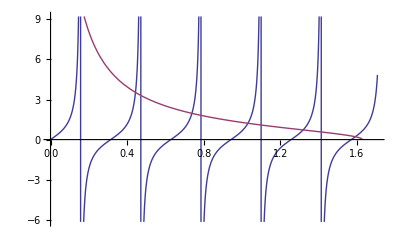

{0.147978,0.44364,0.738329,1.03098,1.31925,1.59191}

{0.454368,4.08391,11.3114,22.0555,36.1133,52.5839}

{1.62134,1.56646,1.45103,1.26004,0.954049,0.341235}

```mathematica
Plot[{Tan[k a],√((U-k^2)/k^2)}, {k,0,√(U 1.1)}]  
Solk=Re[DeleteCases[Table[
If[U>(π/a n)^2,
k/.FindRoot[k Tan[k a]-√(U-k^2), {k,π/a(49/100+n)}]
,0]
,{n,0,10}],0]]
SolE=Table[Solk[[i]]^2 ℏ^2/(2mp),{i,1,Length[Solk]}]
Solk0=Table[√((2 mp)/ℏ^2(V-SolE[[i]])),{i,1,Length[Solk]}]
Solϕ=Table[
Piecewise[{
{Cos[Solk[[i]] a]/Exp[-Solk0[[i]] a] Exp[Solk0[[i]] x],x≤ -a},
{Cos[Solk[[i]] x],-a<x<a},
{Cos[Solk[[i]] a]/Exp[-Solk0[[i]] a] Exp[-Solk0[[i]] x],a≤x}}
],{i,1,Length[Solk]}];
SolϕN=Table[Solϕ[[i]]/(√NIntegrate[Solϕ[[i]]^2,{x,-∞,∞}]),{i,1,Length[Solk]}];
Manipulate[
GraphicsGrid[{{
Plot[{
Solϕ[[n]]+SolE[[n]],
SolE[[n]],
Piecewise[{{V,x≤ -a},{0,-a<x<a},{V,a≤x}}]
},{x,-3a,3a},PlotStyle->{Red,Green,Blue}],
Plot[Evaluate[D[Solϕ[[n]],{x,2}]],{x,-2a,2a}]
}},ImageSize->700],
{n,1,Length[Solk],1}]
```

```mathematica
Join[{{"Eout","Ein","KEout","KE","PE","total E","Eout/(total E)"}},Table[{A1=2NIntegrate[SolϕN[[n]](-ℏ^2/(2mp)Evaluate[D[SolϕN[[n]],{x,2}]]+V SolϕN[[n]]),{x,-∞,-a}],B=NIntegrate[-ℏ^2/(2mp)SolϕN[[n]]Evaluate[D[SolϕN[[n]],{x,2}]],{x,-a,a}],
KEout=2NIntegrate[-ℏ^2/(2mp)SolϕN[[n]]Evaluate[D[SolϕN[[n]],{x,2}]],{x,-∞,-a}],
KE=NIntegrate[-ℏ^2/(2mp)SolϕN[[n]]Evaluate[D[SolϕN[[n]],{x,2}]],{x,-∞,∞}],
PE=NIntegrate[SolϕN[[n]]SolϕN[[n]] Piecewise[{{V,x≤-a},{V,a≤ x}}],{x,-∞,∞}],to=KE+PE,A1/to },{n,1,Length[Solk]}]]//TableForm
```

Eout | Ein | KEout | KE | PE | total E | Eout/(total E)
0.000218066 | 0.45415 | -0.0261782 | 0.427972 | 0.0263963 | 0.454368 | 0.000479932
0.0181968 | 4.06572 | -0.226868 | 3.83885 | 0.245065 | 4.08391 | 0.00445572
0.149984 | 11.1614 | -0.579295 | 10.5821 | 0.729279 | 11.3114 | 0.0132596
0.650308 | 21.4052 | -0.971372 | 20.4338 | 1.62168 | 22.0555 | 0.0294851
2.24963 | 33.8637 | -1.17652 | 32.6872 | 3.42615 | 36.1133 | 0.0622936
11.3939 | 41.19 | -0.52353 | 40.6664 | 11.9174 | 52.5839 | 0.21668

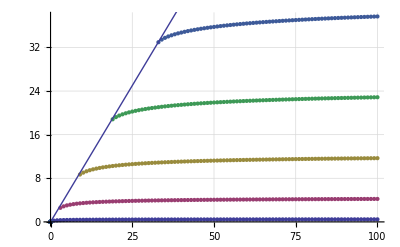

```mathematica
a=10;
SolE2=Table[
If[(2 mp)/ℏ^2 V>(π/a n)^2,
{V,(*E-V*)(k^2 ℏ^2/(2mp))/.FindRoot[k Tan[k a]-√( (2 mp)/ℏ^2 V-k^2), {k,π/a(49/100+n)}]}
,{0,0}]
,{n,0,4},{V,1,100,1}];
Show[
ListPlot[DeleteCases[DeleteCases[SolE2,{0,0}2],{},1],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]],
Plot[x,{x,0,100}]
]
```

```mathematica
Manipulate[
Plot[{Tan[k a],√((U-k^2)/k^2)}, {k,0,2},PlotRange->{0,100}] 
,{{a,10},1,20}
,{{U,100},1,600}
]
```